Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                             < >    Ξ

Edited by Hao Feng

## 2 Descriptive Statistics and Probability Theory

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 1 of the book [1] titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation. This chapter also serves as a summary of the book titled Statistics for Machine Learning with Mathematica Applications. For detailed proofs of theorems, additional examples, and comprehensive explanations, including Mathematica applications, please refer to Ref [2].”

Descriptive statistics form the foundational toolset for summarizing and interpreting data, offering insights into central tendencies and variability within datasets [3-10]. It serves as the initial lens through which raw data is scrutinized, paving the way for more advanced analyses. On the other hand, probability theory plays a crucial role in quantifying uncertainty and randomness inherent in data. It underpins the probabilistic nature of real-world phenomena, intertwining with statistical measures to create a comprehensive framework for data analysis.

In artificial intelligence (AI) applications, probability theory serves two fundamental purposes:

1. Guiding the rationale behind AI reasoning processes, shaping algorithmic design to compute or approximate expressions derived from probability.

2. Providing an analytical framework to dissect and evaluate AI system behavior, assessing performance under diverse conditions and the implications of algorithmic choices.

By integrating probability and statistics in AI development, researchers gain insights into theoretical foundations, contributing to the refinement and optimization of intelligent systems.

Mathematica provides powerful tools for analyzing and visualizing data, including built-in functions for random sampling, order and count statistics, frequency distributions, and distribution shapes. By using these functions, you can gain insights into your data, identify patterns and outliers, and make informed decisions based on statistical analysis. Additionally, Mathematica offers various functions to compute central tendency, dispersion and shape measures. These functions provide quick and accurate calculations for determining the typical or central value of a dataset and for visualizing location statistics.

• Random sampling is a method of selecting a subset of individuals or data points from a larger population in a way that each member of the population has an equal chance of being selected. In Mathematica, you can use built-in functions such as RandomSample and RandomChoice to generate random samples from a dataset or population. These functions can be useful for testing hypotheses, simulating experiments, and exploring datasets.

• Also, you can use the built-in function Histogram to generate a histogram of the frequency distribution of a dataset.

• Moreover, you can use the built-in functions PDF, and CDF, to visualize the shape of a distribution.

• The Mean function in Mathematica calculates the arithmetic mean of a list of numbers. It is a commonly used measure of central tendency and provides the average value of the dataset.

• The Median function computes the middle value of a sorted dataset. It is useful for finding a representative value that is not influenced by extreme values or outliers.

• The Commonest function determines the mode(s) of a dataset, which represents the most frequently occurring value(s). This can be useful when dealing with categorical or discrete data.

• Mathematica provides functions like Quartiles and Quantile to calculate specific quantiles of a dataset. These functions allow you to find values that divide the dataset into equal proportions, such as the first quartile (25th percentile) or the median (50th percentile).

• The TrimmedMean function in Mathematica calculates the mean of a dataset after excluding a specified percentage of extreme values from both ends. It can be useful in situations where outliers may significantly affect the overall mean.

• The WinsorizedMean function provides a robust measure of central tendency by reducing the impact of outliers or extreme values on the calculated mean. It achieves this by replacing extreme values with values from a specified percentile.

• Both the HarmonicMean and GeometricMean functions provide alternative measures of central tendency that are suitable for specific types of data. While the HarmonicMean is useful for rates and ratios, the GeometricMean is applicable for multiplicative relationships and positive values.

• Mathematica offers built-in functions for visualizing location statistics. For example, you can create box plots using BoxWhiskerChart to display the median, quartiles, and potential outliers in a dataset.

• The InterquartileRange function calculates the range between the upper quartile and the lower quartile in a dataset. It is useful for identifying the spread or dispersion of the middle 50% of the data.

• The QuartileDeviation function calculates the semi-interquartile range, which is half of the Interquartile Range. It provides a measure of dispersion around the median and is less affected by extreme values.

• The MeanDeviation function computes the average absolute deviation of each data point from the mean. It gives an indication of the average distance between individual data points and the mean. MeanDeviation is less influenced by extreme values and provides a robust measure of dispersion.

• The StandardDeviation function calculates the standard deviation, which is a widely used measure of dispersion. It quantifies the amount of variation or spread in a dataset by measuring the average distance between each data point and the mean. A higher standard deviation indicates greater variability.

• The Variance function computes the average squared deviation of each data point from the mean. It provides a measure of the overall variability in a dataset.

• The TrimmedVariance function calculates the variance after trimming a certain percentage of extreme values from both ends of the dataset. Trimming reduces the impact of outliers and extreme values on the variance calculation, providing a more robust measure of dispersion.

• The WinsorizedVariance function is similar to TrimmedVariance, but instead of removing extreme values, it replaces them with values closer to the mean.

• The Moment function computes the nth moment of a dataset.

• The CentralMoment function calculates the nth central moment of a dataset. It measures the dispersion of data around the mean.

• FactorialMoment function computes the nth factorial moment of a dataset.

• The Skewness function measures the asymmetry of a dataset’s distribution. It indicates whether the dataset is skewed to the left (negative skewness) or to the right (positive skewness) relative to the mean.

• The QuartileSkewness function is a measure of skewness based on quartiles.

• The Kurtosis function measures the peakedness or flatness of a dataset’s distribution. It provides insights into the tail behavior and presence of outliers.

The chapter will include practical examples and exercises to reinforce the concepts learned. By the end of this chapter, you will be equipped with the knowledge and skills to perform descriptive statistical analysis using Mathematica, making it easier to summarize and interpret data effectively.

Moreover, we will delve into the world of discrete random variables, which play a crucial role in modeling various phenomena with countable outcomes. We explore their Probability Mass Functions (PMFs), Cumulative Density Functions (CDFs), and Moment Generating Functions (MGFs), while leveraging the power of Mathematica to perform computations and gain insights.

• PDF and CDF assist in determining the probability density and cumulative probability of discrete random variables, respectively.

• Expectation and NExpectation functions calculate the expected value or mean of a discrete random variable, providing insights into its central tendency.

• MomentGeneratingFunction and CentralMomentGeneratingFunction allow for the calculation of higher-order moments and central moments, offering a more comprehensive understanding of the distribution of the random variable.

• Mathematica offers a comprehensive set of built-in functions to handle various probability distributions effortlessly. In this chapter, we also explore two essential probability distributions: Binomial distribution, and discrete uniform distribution.

Additionally, we explore the world of continuous random variables, which are essential for modeling phenomena with uncountable outcomes. We study the continuous probability distributions, exploring their Probability Density Functions (PDFs), CDFs, and MGFs. We will demonstrate how to define, manipulate, and analyze continuous random variables and probability distributions using Mathematica’s syntax and functionality. We will study two fundamental probability distributions: Normal distribution, and uniform distribution.

By engaging in hands-on exercises and experimenting with different scenarios, readers will enhance their understanding of the concepts and develop proficiency in utilizing Mathematica for probability analysis.

### Descriptive Statistics

Mathematica provides a wide range of functions for generating different types of random data, such as integers, real numbers, vectors, matrices, and graphs which can be useful for a several applications, such as simulations, modeling, and data analysis.

1. When generating random data, it is important to specify the range and distribution of the data. For example, you can use the UniformDistribution function to generate data uniformly distributed between a specified minimum and maximum value, or the NormalDistribution function to generate data following a normal distribution with a specified mean and standard deviation.

2. The random data generated by Mathematica’s built-in functions is pseudo-random, meaning that the sequence of numbers generated is deterministic and depends on the seed value. It is important to set a specific seed value using the SeedRandom function if you want to reproduce the same sequence of random numbers.

3. One of the key advantages of Mathematica’s random data generation functions is their integration with other mathematical and statistical functions in the program. This allows users to easily incorporate generated

code 2.1 RandomInteger

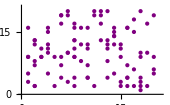

```mathematica
(* This code generates random data fro a scatter plot by using the RandomInteger function with the interval {1, 20}. The data variable is a list of n pairs of random values generated using the Table function. The data is plotted using the ListPlot function: *)

n=100;
data=Table[{RandomInteger[{1,20}],RandomInteger[{1,20}]},{n}];

ListPlot[
data,
PlotRange->{{0,21},{0,21}},
PlotStyle->Directive[Purple,PointSize[Medium]],
ImageSize->170
]
```

code 2.2 RandomReal

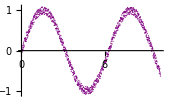

```mathematica
(*This code generates random data points for a smooth curve by adding random noise to the function Sin[x].The RandomReal function with the interval {-0.1,0.1} is used to generate random noise.The data variable is a list of x and y values generated using the Table function with a step size of 10/n.The data points are plotted using the ListPlot function with the PlotRange option set to All:*)

n=1000;
data=Table[{x,Sin[x]+RandomReal[{-0.1,0.1}]},{x,0,10,10/n}];

ListPlot[
data,
PlotRange->All,
PlotStyle->Purple,
ImageSize->170
]
```

code 2.3 RandomPoint

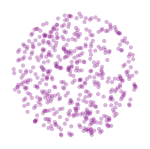

```mathematica
(* Generate a list of points in a unit disk: *)

pts=RandomPoint[Disk[],500];

Graphics[
{PointSize[0.02],Purple,Opacity[0.3],Point[pts]},
ImageSize->150
]
```

code 2.4 RandomChoice

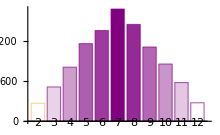

```mathematica
(*This code uses the RandomChoice function to generate 10000 rolls of two six-sided dice, sums the values of the dice, and stores the results in the variable rolls.It then creates a table counts of the number of times each possible sum occurs, from 2 to 12. Finally, it displays the frequency of each sum using a BarChart with labeled bars:*)

rolls=Table[
RandomChoice[Range[6]]+RandomChoice[Range[6]],
{10000}
];

counts=Table[
Count[rolls,i],{i,2,12}
];

BarChart[
counts,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ChartLabels->Range[2,12],
ImageSize->220
]
```

code 2.5 RandomSample

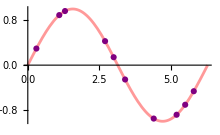

```mathematica
(*This code plots the sine function f[x] between 0 and 2 Pi,and then superimposes 10 Purple points on the plot.These points are randomly sampled from a list of equidistant points on the function.The RandomSample function is called with the list of points as the first argument,and 10 as the second argument to select 10 random points from the list:*)

f[x_]:=Sin[x];
Plot[
f[x],{x,0,2π},
PlotStyle->{Red,Opacity[0.4]},
Epilog->{
PointSize[0.02],
Purple,
Point[
RandomSample[
Table[{x,f[x]},{x,0,2π,0.1}],
10]
]
},
ImageSize->220
]
```

code 2.6 RandomVariate

```mathematica
(*The code uses the Table function to generate a list of n random variables drawn from a normal distribution with mean mu and standard deviation sigma using the RandomVariate function.This list is then passed to ListPlot to create the plot.The Manipulate function allows for interactive exploration of the plot by adjusting the values of n,mu,and sigma.This code can be used as a starting point for more advanced statistical simulations and explorations.For example,one could modify the code to simulate data from a different distribution,or to add additional controls for exploring different aspects of the distribution (such as skewness or kurtosis):*)

Manipulate[
ListPlot[
Table[
RandomVariate[NormalDistribution[μ,σ]],
{n}
],
Filling->Axis,
PlotStyle->{Directive[Purple,Opacity[0.8]]},
PlotRange->{{0,100},{-10,10}},
ImageSize->300
],
{{n,50},1,100,1},
{{μ,0},-5,5,0.1},
{{σ,1},0.1,5,0.1}
]
```

Some of the most commonly used Mathematica functions include Histogram, and Histogram3D. By using these functions, you can gain a deeper understanding of the underlying patterns in your data and make informed decisions based on your findings.

code 2.7 Histogram

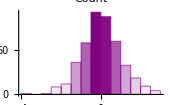
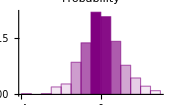
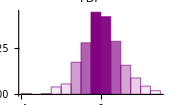
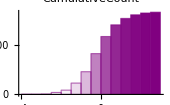
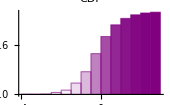
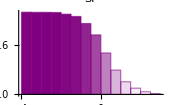

```mathematica
(*This code generates six histograms of 500 random samples drawn from a normal distribution with mean 0 and standard deviation 1,using different methods to set the vertical scale of the histograms.The different methods used are:"Count","Probability","PDF","CumulativeCount","CDF",and "SF".This allows for a comparison of different ways of visualizing the same data,which can help in understanding the data and selecting the most appropriate method for a particular analysis:*)

sampledata=RandomVariate[
NormalDistribution[0,1],
500
];

Table[
Histogram[
sampledata,
Automatic,
heightmethod,
PlotLabel->heightmethod,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->170
],
{heightmethod,{"Count","Probability","PDF","CumulativeCount","CDF","SF"}}
]
```

code 2.8 Histogram

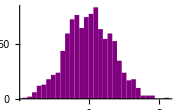

```mathematica
(*This code generates a histogram of 1000 random samples drawn from a normal distribution with mean 0 and standard deviation 1. The resulting histogram has no outline or borders around the bars and is colored in purple.Without the borders around the bars,the shape of the distribution may be more apparent.This can be especially useful when comparing multiple histograms with different data sets or parameters:*)

Histogram[
RandomVariate[
NormalDistribution[0,1],
1000
],
ChartBaseStyle->EdgeForm[None],
ChartStyle->Purple,
ImageSize->179
]
```

code 2.9 Histogram3D

```mathematica
(*This code generates a sequence of 3D histograms for a random sample of size 300 from a bivariate normal distribution with mean 0 and standard deviation 1 in each dimension.The use of different height functions allows for a more comprehensive understanding of the sample's distribution and provides a range of useful visualization tools for data analysis:*)

sampledata=RandomVariate[
NormalDistribution[0,1],
{300,2}
];

Table[
Histogram3D[
sampledata,
Automatic,
height,
PlotLabel->height,
ColorFunction->Function[{height},Opacity[0.9]],
ChartStyle->RGBColor[0.6,0.30,0.60],
ImageSize->170
],
{height,{"Count","Probability","PDF","CDF","SF","HF"}}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

The Wolfram Language’s descriptive statistics functions operate both on explicit data and on symbolic representations of statistical distributions, making it a valuable tool for data analysis and exploratory data science tasks.

code 2.10 Mean

127.

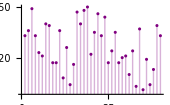

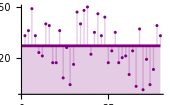

```mathematica
(*The code analyzes a dataset of heights by calculating the mean and generating two plots.The first plot displays the data set, while the second plot displays the data set along with horizontal line for the mean:*)

h={133,136,149,133,123,121,140,139,117,117,136,108,126,104,116,147,140,148,150,122,135,146,133,144,117,124,135,117,120,121,110,124,103,137,101,119,104,113,139,133};

m=N[Mean[h]]
n=Length[h];

ListPlot[
h,
Filling->Axis,
PlotStyle->Purple,
ImageSize->170
]

ListPlot[
{h,{{0,m},{n,m}}},
Joined->{False,True},
Filling->{1->m,2->Axis},
PlotStyle->Purple,
ImageSize->170,
PlotLegends->{None,"Mean =127"}
]
```

code 2.11 Commonest

{{133,4},{136,2},{149,1},{123,1},{121,2},{140,2},{139,2},{117,4},{108,1},{126,1},{104,2},{116,1},{147,1},{148,1},{150,1},{122,1},{135,2},{146,1},{144,1},{124,2},{120,1},{110,1},{103,1},{137,1},{101,1},{119,1},{113,1}}

{101.,103.,104.,108.,110.,113.,116.,117.,119.,120.,121.,122.,123.,124.,126.,133.,135.,136.,137.,139.,140.,144.,146.,147.,148.,149.,150.}

127

-Graphics-

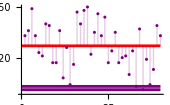

```mathematica
(*The code reads in a dataset h of heights and calculates Commonest elements.It then produces two plots:a scatter plot of the dataset h,and a plot that shows both h and three horizontal lines at the commonest elements and mean.These plots are used for visualizing the distribution of the dataset and highlighting the location of the commonest elements and mean:*)

h={133,136,149,133,123,121,140,139,117,117,136,108,126,104,116,147,140,148,150,122,135,146,133,144,117,124,135,117,120,121,110,124,103,137,101,119,104,113,139,133};

Tally[h]
c=N[Complement[h]]
m=Mean[h]
n=Length[h];

ListPlot[
h,
Filling->Axis,
PlotStyle->Purple,
ImageSize->170
]

ListPlot[
{h,{{0,c[[1]]},{n,c[[1]]}},{{0,c[[2]]},{n,c[[2]]}},{{0,m},{n,m}}},
Joined->{False,True,True,True},
Filling->{1->m,2->{3}},
PlotStyle->{Purple,Purple,Purple,Red},
ImageSize->170,
PlotLegends->{"h","Commonest=133","Commonest=117","Mean =127"}
]
```

code 2.12 HarmonicMean, GeometricMean and Mean

{4.05091,4.96548,5.76365}

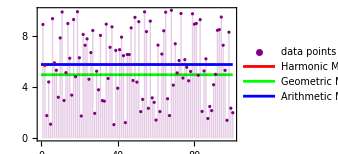

```mathematica
(*The code will generate a list of random numbers,calculate their Harmonic Mean,Geometric Mean,and Arithmetic Mean,and then plot the means against the number of elements in the list.For positive data,we can see that Harmonic Mean<=Geometric Mean<=Arithmetic Mean:*)

SeedRandom[1234];
n=100;
d=RandomReal[{1,10},n];
hm=HarmonicMean[d];
gm=GeometricMean[d];
am=Mean[d];
means={hm,gm,am}
labels={"data points","Harmonic Mean","Geometric Mean","Arithmetic Mean"};

plot=ListPlot[
{d,{{0,hm},{h,hm}},{{0,gm},{n,gm}},{{0,am},{n,am}}},
Joined->{False,True,True,True},
Filling->{1->Axis},
Frame->True,
PlotRange->All,
PlotStyle->{Purple,Red,Green,Blue},
PlotLegends->labels,
ImageSize->250
]
```

The Mathematica function BoxWhiskerChart is a powerful tool for visualizing and analyzing data distributions. Here are some features of this function:

• Clear representation of data: BoxWhiskerChart provides a clear and concise representation of the distribution of a dataset. It displays important statistical measures such as the median, quartiles, and outliers, making it easy to understand the central tendency and spread of the data.

• Customizable appearance: The function offers a wide range of options to customize the appearance of the box-and-whisker plot. You can adjust the colors, styles, and sizes of the boxes, whiskers, outliers, and other elements to suit your preferences or match your presentation or publication style.

• Comparative analysis: BoxWhiskerChart allows for easy comparison of multiple datasets. You can plot several box-and-whisker diagrams side by side or in a stacked manner, making it straightforward to identify differences or similarities in distributions.

• Interaction and exploration: The resulting chart is interactive, meaning you can hover over different elements to obtain more detailed information about specific data points or summary statistics. This interactivity enhances the exploratory data analysis process and allows for a deeper understanding of the underlying distribution.

BoxWhiskerChart draws a box-and-whisker summary of the distribution of values in each datai. See the following figure

-Graphics-

code 2.13 BoxWhiskerChart

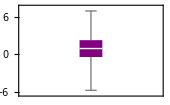

```mathematica
(*The code uses the RandomVariate function to generate a data vector with 200 values.It samples from a normal distribution with a mean of 1 and a standard deviation of 2. then,the code generates a basic box-and-whisker chart using randomly generated data:*)

BoxWhiskerChart[
RandomVariate[
NormalDistribution[1,2],
200
],
ChartStyle->Purple,
ImageSize->170
]
```

code 2.14 BoxWhiskChart

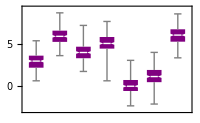

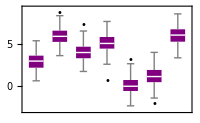

```mathematica
(*The code demonstrates customization options for a box-and-whisker chart.It generates a list of seven datasets,each containing 200 data points randomly sampled from normal distributions.The mean of each dataset is randomly chosen from the integers 0 to 6,while the standard deviation is fixed at 1. The first BoxWhiskerChart call creates a notched box-and-whisker chart,displaying confidence intervals around the medians of each dataset.The second BoxWhiskerChart call explicitly shows outliers,highlighting extreme or unusual data points:*)

data=Table[
RandomVariate[
NormalDistribution[RandomInteger[6],1],
200
],
{7}
];

BoxWhiskerChart[
data,
"Notched",
ChartStyle->Purple,
ImageSize->200
]

BoxWhiskerChart[
data,
"Outliers",
ChartStyle->Purple,
ImageSize->200
]
```

code 2.15 BoxWhiskerChart

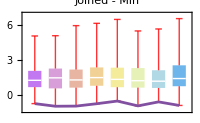
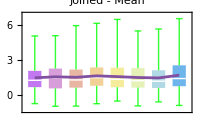
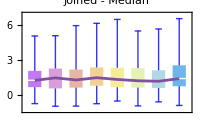
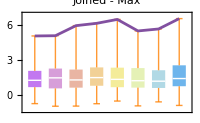

```mathematica
(*The code generates a series of BoxWhiskerCharts to visualize the distribution of a dataset called'data' using the SkewNormalDistribution.The dataset has dimensions 8 rows by 200 columns.The code uses the BoxWhiskerChart function to create a box and whisker plot for each column in the'data' dataset.Each chart represents statistical measures such as the minimum,mean,median,and maximum values with different line styles and colors:*)

data=RandomVariate[
SkewNormalDistribution[0,2,4],
{8,200}
];

Table[
BoxWhiskerChart[
data,
{
{"Whiskers",Directive[Thick,s[[2]],Opacity[0.8]]},
{"Fences",Directive[Thick,s[[2]],Opacity[0.8]]}
},
Joined->s[[1]],
PlotLabel->Style[Row[{"Joined - ",s[[1]]}]],
ChartStyle->"Pastel",
ImageSize->200
],
{s,{{"Min",Red},{"Mean",Green},{"Median",Blue},{"Max",Orange}}}
]
```

code 2.16 BoxWhiskerChart

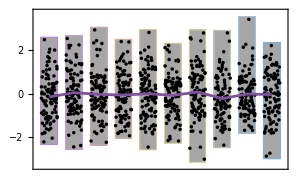
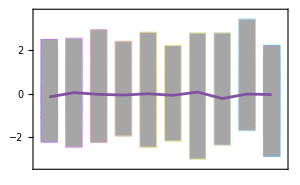

```mathematica
(*The code generates multiple density plots using the DistributionChart function.It generates a 2D array of random data called data.It consists of 10 rows and 100 columns,where each element is sampled from a standard normal distribution.The code then uses a combination of Table and DistributionChart to generate density plots for each element in the list of chart element functions.The Joined option is set to "Mean" to connect the mean values of the distributions with a line.The ChartElementFunction option is used to specify different chart element functions,such as "PointDensity" and "LineDensity".*)

data=RandomVariate[NormalDistribution[],{10,100}];

Table[
DistributionChart[
data,
Joined->"Mean",
ChartElementFunction->s,
ChartStyle->"Pastel",
ImageSize->300
],
{s,{"PointDensity","LineDensity"}}
]
```

code 2.17 BoxWhiskerChart

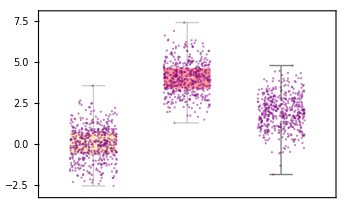

```mathematica
(*The code generates three sets of random data (data1,data2,data3) by sampling from a normal distribution with different means (μ) using RandomVariate.Each set consists of 500 data points.The BoxWhiskerChart function is used to create a box-and-whisker plot.The Epilog option is used to add additional elements to the chart.In this code,points are overlaid on the chart to represent the individual data points of each dataset.The points are created using Map and Transpose.The random displacement in the x-axis is in a range of-0.25 to 0.25:*)

{data1,data2,data3}=Table[
RandomVariate[NormalDistribution[μ,1],500],
{μ,{0,4,2}}
];
BoxWhiskerChart[
{data1,data2,data3},
ChartStyle->{Directive[BLue,Opacity[0.4]],Directive[Red,Opacity[0.4]],Directive[White,EdgeForm[Thickness[0.001]]]},
ImageSize->350,
Epilog->{
Directive[Purple,Opacity[0.5]],
PointSize[0.0045],
Map[
Point,{
Transpose[{ConstantArray[1,Length[data1]]+RandomReal[{-0.25,0.25},Length[data1]],data1}],
Transpose[{ConstantArray[2,Length[data2]]+RandomReal[{-0.25,0.25},Length[data2]],data2}],
Transpose[{ConstantArray[3,Length[data3]]+RandomReal[{-0.25,0.25},Length[data3]],data3}]}
]
}
]
```

Dispersion statistics summarize the scatter or spread of the data. Most of these functions describe deviation from a particular location. For instance, variance is a measure of deviation from the mean. Mathematica provides a set of functions and tools for calculating, visualizing, and analyzing dispersion statistics, allowing users to gain deeper insights into the variability and distribution of their data. Let us go through them in detail.